```mathematica
Clear["Global`*"]
```

```mathematica
(*degree of polynomial/precision of quadrature:*)
degree=7;
(*Number of quadrature points:*)
Ng=13;
(*Make sure (degree+1)(degree+2)/2 <= 3Ng*)
```

```mathematica
eqns=Flatten[Table[If[i+j>degree,0,1/2∑_(k=1)^Ng w[k] ξ[k]^i η[k]^j==(i! j!)/((i+j+2)!)],{i,0,degree},{j,0,degree}],1];
eqns=DeleteCases[eqns,0];
(*Below output should be one:*)
(eqns//Length)/((degree+1)(degree+2)/2)
```

1

```mathematica
eqns//Length
3 Ng
```

36

39

```mathematica
Ng
```

13

```mathematica
eqns=Flatten[Table[If[i+j>degree,0,1/2∑_(k=1)^Ng w[k] ξ[k]^i η[k]^j==(i! j!)/((i+j+2)!)],{i,0,degree},{j,0,degree}],1];
eqns=DeleteCases[eqns,0];
nLine1=6;(*nLine/2 are no. of points in line1*)
nLine2=3;
symCond1=Table[{η[k]==ξ[k]},{k,1,nLine1}]//Flatten
symCond2=Table[{η[k]==-2(ξ[k]-1/2),η[k]!=ξ[k]},{k,nLine1+1,nLine1+nLine2}]//Flatten
symCond3=Table[{η[k+1]==ξ[k],ξ[k+1]==η[k]},{k,1,Ng-1,2}]//Flatten
bound=Table[{η[k]<=1,η[k]>=0,ξ[k]<=1,ξ[k]>=0},{k,1,Ng}]//Flatten
```

```mathematica
eqns=Flatten[Table[If[i+j>degree,0,1/2∑_(k=1)^Ng w[k] ξ[k]^i η[k]^j==(i! j!)/((i+j+2)!)],{i,0,degree},{j,0,degree}],1];
eqns=DeleteCases[eqns,0];
nLine1=3;(*nLine/2 are no. of points in line1*)
nLine2=3;
symCond1=Table[{η[k]==ξ[k]},{k,1,nLine1}]//Flatten
symCond2={η[1]==1/3,ξ[1]==1/3}
symCond3=Table[{η[k+1]==ξ[k],ξ[k+1]==η[k]},{k,nLine1+1,Ng-1,2}]//Flatten
symCond4={η[4]==η[2],ξ[5]==ξ[2],η[6]==η[3],ξ[7]==ξ[3]}
bound=Table[{η[k]<=1,η[k]>=0,ξ[k]<=1,ξ[k]>=0},{k,1,Ng}]//Flatten
```

{η[1]==ξ[1],η[2]==ξ[2],η[3]==ξ[3]}

{η[1]==1/3,ξ[1]==1/3}

{η[5]==ξ[4],ξ[5]==η[4],η[7]==ξ[6],ξ[7]==η[6],η[9]==ξ[8],ξ[9]==η[8],η[11]==ξ[10],ξ[11]==η[10],η[13]==ξ[12],ξ[13]==η[12]}

{η[4]==η[2],ξ[5]==ξ[2],η[6]==η[3],ξ[7]==ξ[3]}

{η[1]≤1,η[1]≥0,ξ[1]≤1,ξ[1]≥0,η[2]≤1,η[2]≥0,ξ[2]≤1,ξ[2]≥0,η[3]≤1,η[3]≥0,ξ[3]≤1,ξ[3]≥0,η[4]≤1,η[4]≥0,ξ[4]≤1,ξ[4]≥0,η[5]≤1,η[5]≥0,ξ[5]≤1,ξ[5]≥0,η[6]≤1,η[6]≥0,ξ[6]≤1,ξ[6]≥0,η[7]≤1,η[7]≥0,ξ[7]≤1,ξ[7]≥0,η[8]≤1,η[8]≥0,ξ[8]≤1,ξ[8]≥0,η[9]≤1,η[9]≥0,ξ[9]≤1,ξ[9]≥0,η[10]≤1,η[10]≥0,ξ[10]≤1,ξ[10]≥0,η[11]≤1,η[11]≥0,ξ[11]≤1,ξ[11]≥0,η[12]≤1,η[12]≥0,ξ[12]≤1,ξ[12]≥0,η[13]≤1,η[13]≥0,ξ[13]≤1,ξ[13]≥0}

```mathematica
Ng
```

13

```mathematica
eqns=Join[eqns,symCond1,symCond2,symCond3,bound];
```

```mathematica
eqns//Length
3 Ng
```

103

39

```mathematica
sol=NSolve[eqns,Table[{w[k],ξ[k],η[k]},{k,1,Ng}]//Flatten,Reals,WorkingPrecision->20]
```

$Aborted

```mathematica
Length@sol
```

24

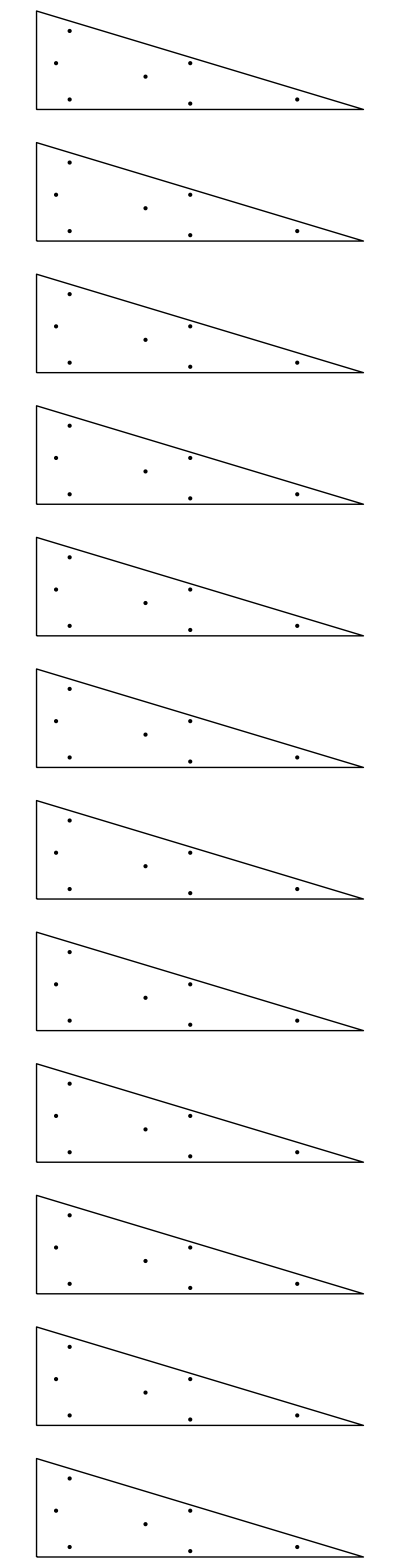

```mathematica
GraphicsColumn[Table[Graphics[{Point[Table[{η[k],ξ[k]}/.sol[[p]],{k,1,Ng}]],Line[{{0,0},{0,1},{1,0},{0,0}}]}],{p,1,Length@sol/2}]]
```

```mathematica
fTest[x_,y_]:=Cos[x]Sin[y^2];
```

```mathematica
NIntegrate[fTest[x,y],{x,0,1},{y,0,1-x}]
```

0.0777232

```mathematica
N[(1/2∑_(k=1)^Ng w[k] fTest[ξ[k],η[k]]/.sol[[1]]),20]
```

0.077723015753128691799

```mathematica
(1/2∑_(k=1)^Ng w[k] fTest[ξ[k],η[k]]/.sol[[1]])//N
```

0.077723

```mathematica
(1/2∑_(k=1)^Ng w[k] fTest[ξ[k],η[k]]/.sol[[1]])//RepeatedTiming
```

{0.0000567589,0.1505843693132346482}